```mathematica
f[x_]:=Abs[x];
n=4;
a=-π//N;
b=π//N;
φ[x_,k_Integer]:=If[k==0,1/N[√(2π)],If[Mod[k,2]==1,Cos[(k+1) x/2]/N[√π],Sin[k x/2]/N[√π]]];
α[k_Integer]:=∫_a^b f[x] φ[x,k]ⅆx;
px=Simplify[∑_(k=0)^(2n) α[k] φ[x,k]];
xi[i_Integer]:=a+i(b-a)/(2n);
L[j_Integer,x_]:=(∏_(k=0)^(j-1) (x-xi[k])/(xi[j]-xi[k])) (∏_(k=j+1)^(2n) (x-xi[k])/(xi[j]-xi[k]));
ipx=Simplify[∑_(j=0)^(2n) f[xi[j]] L[j,x]];
p1=Plot[f[x],{x,a,b},DisplayFunction->Identity];
p2=Plot[px/.x->t,{t,a,b},DisplayFunction->Identity,PlotStyle->RGBColor[1,0,0]];
p3=Plot[ipx/.x->t,{t,a,b},DisplayFunction->Identity,PlotStyle->RGBColor[0,0,1]];
Show[p1,p2,p3,DisplayFunction->$DisplayFunction,Frame->True,PlotRange->All]
E21=∫_a^b (f[x]-px)^2ⅆx//N
E22=∫_a^b (f[x]-ipx)^2ⅆx//N
```

```mathematica
n=3
```

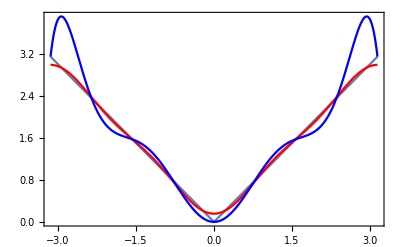

0.0118786

0.786443

```mathematica
n=2
```

0.0747546+0. ⅈ

0.535911